# Registration of identified sources in image and alignment to Yale Catalog

## Importing the source positions and the visible bright stars from python generated CSV

```mathematica
sources=Import[NotebookDirectory[]<>"sources.csv"];
(*Rescale source intensities to magnitude scale with arbitrary offset*)
sources={#⟦1⟧,#⟦2⟧,-2.5Log10[#⟦3⟧/Max[sources⟦;;,3⟧]]}&/@sources;
yale=Import[NotebookDirectory[]<>"yale.csv"];
```

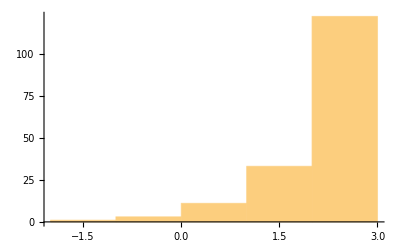

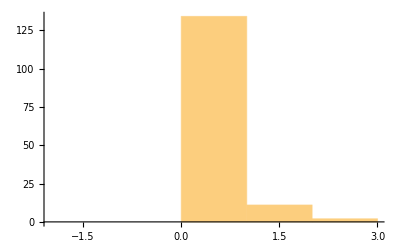

```mathematica
Histogram[yale⟦;;,3⟧,{-2,3,1}]
Histogram[sources⟦;;,3⟧,{-2,3,1}]
```

```mathematica
Min[yale⟦;;,2⟧]
```

-88.9564

## Projection used for Fisheye

```mathematica
Cases[Reduce[r==f ((1-Z)Sin[θ])/(Cos[θ]-Z),θ]/.C[1]->0,θ==_,Infinity]⟦-2;;⟧
%/.{f->1.55,Z->0.6,r->1}
```

{θ==2 ArcTan[(-f+f Z-√(-(-1+Z) (f^2+r^2-f^2 Z+r^2 Z)))/(r (1+Z))],θ==2 ArcTan[(-f+f Z+√(-(-1+Z) (f^2+r^2-f^2 Z+r^2 Z)))/(r (1+Z))]}

{θ==-1.59068,θ==0.480684}

```mathematica
2 ArcTan[f(-1+Z+√((1-Z)^2+(r/f)^2(1-Z^2)))/(r (1+Z))]
```

```mathematica
Factor[f(-1+Z+√((1-Z)^2+(r/f)^2(1-Z^2)))/(r (1+Z))]
```

(f (-1+Z+√(((-1+Z) (-f^2-r^2+f^2 Z-r^2 Z))/f^2)))/(r (1+Z))

```mathematica
f ((1-Z)Sin[θ])/(Cos[θ]-Z)/.Z->0
```

f Tan[θ]

## Transformation from horizontal frame to sensor frame

```mathematica
transform=Simplify[TrigExpand[p == {r Cos[ϕ]+xc, r Sin[ϕ]+yc}/.{ϕ->A+ϕN,r->f Piecewise[{{Sin[k θ]/k, k<0}, {θ, k==0}, {Tan[k θ]/k, Z≠0}, {((1-Z)Sin[θ])/(Cos[θ]-Z), True}}]}]/.({Sin[A]->-Sin[H]Cos[δ]/Cos[a],Cos[A]->(Sin[δ]-Sin[φ]Sin[a])/(Cos[φ]Cos[a])}/.a->π/2-θ)/.θ->ArcCos[Sin[δ]Sin[φ]+Cos[δ]Cos[φ]Cos[H]]]
```

p=={1/(√(1-(Cos[H] Cos[δ] Cos[φ]+Sin[δ] Sin[φ])^2))(xc √(1-Cos[H]^2 Cos[δ]^2 Cos[φ]^2-2 Cos[H] Cos[δ] Cos[φ] Sin[δ] Sin[φ]-Sin[δ]^2 Sin[φ]^2)+f (Piecewise[{{Sin[k ArcCos[Cos[H] Cos[δ] Cos[φ]+Sin[δ] Sin[φ]]]/k, k<0}, {ArcCos[Cos[H] Cos[δ] Cos[φ]+Sin[δ] Sin[φ]], k==0}, {Tan[k ArcCos[Cos[H] Cos[δ] Cos[φ]+Sin[δ] Sin[φ]]]/k, Z≠0}, {((1-Z) √(1-(Cos[H] Cos[δ] Cos[φ]+Sin[δ] Sin[φ])^2))/(-Z+Cos[H] Cos[δ] Cos[φ]+Sin[δ] Sin[φ]), True}}]) (Cos[δ] Sin[H] Sin[ϕN]+Cos[ϕN] (Sec[φ] Sin[δ]-Sin[φ] (Cos[H] Cos[δ]+Sin[δ] Tan[φ])))),1/(√(1-(Cos[H] Cos[δ] Cos[φ]+Sin[δ] Sin[φ])^2))(yc √(1-Cos[H]^2 Cos[δ]^2 Cos[φ]^2-2 Cos[H] Cos[δ] Cos[φ] Sin[δ] Sin[φ]-Sin[δ]^2 Sin[φ]^2)+f (Piecewise[{{Sin[k ArcCos[Cos[H] Cos[δ] Cos[φ]+Sin[δ] Sin[φ]]]/k, k<0}, {ArcCos[Cos[H] Cos[δ] Cos[φ]+Sin[δ] Sin[φ]], k==0}, {Tan[k ArcCos[Cos[H] Cos[δ] Cos[φ]+Sin[δ] Sin[φ]]]/k, Z≠0}, {((1-Z) √(1-(Cos[H] Cos[δ] Cos[φ]+Sin[δ] Sin[φ])^2))/(-Z+Cos[H] Cos[δ] Cos[φ]+Sin[δ] Sin[φ]), True}}]) (Cos[φ] Sin[δ] Sin[ϕN]-Cos[δ] (Cos[ϕN] Sin[H]+Cos[H] Sin[φ] Sin[ϕN])))}

```mathematica
Simplify[(transform/.{φ->49.°,f->1.55,δ->50°,k->-1,xc->770/1000*2.4,yc->887/1000*2.4,Z->0,ϕN->π/2-8°})//N]
```

p=={0.108414-0.104649 Cos[H]-(10.3916 √(0.665753-0.487612 Cos[H]-0.177836 Cos[H]^2) √(0.665753-0.487612 Cos[H]-0.177836 Cos[H]^2))/(-3.74362+2.74191 Cos[H]+1. Cos[H]^2)+0.986625 Sin[H],0.771403-0.744615 Cos[H]-(11.9705 √(0.665753-0.487612 Cos[H]-0.177836 Cos[H]^2) √(0.665753-0.487612 Cos[H]-0.177836 Cos[H]^2))/(-3.74362+2.74191 Cos[H]+1. Cos[H]^2)-0.138661 Sin[H]}

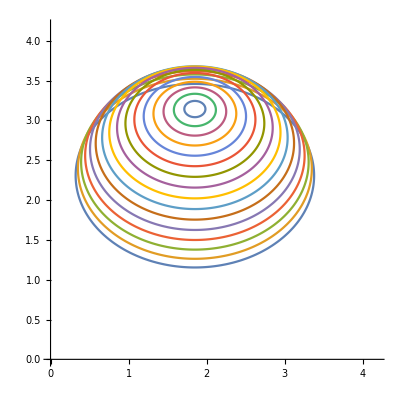

```mathematica
ParametricPlot[Evaluate[Table[transform⟦2⟧/.{φ->49.°,f->1.55,δ->d,k->-1,xc->770/1000*2.4,yc->887/1000*2.4,Z->-2.2,ϕN->π/2},{d,10°,85°,5°}]],{H,0,2π},PlotRange->{{0,1744/1000*2.4},{0,1740/1000*2.4}},AspectRatio->1]
```

```mathematica
Expand[FullSimplify[PiecewiseExpand[transform⟦2⟧,k<0]/.{k->-1,ϕN->π/2}],H]/.{-f Cos[δ]Sin[φ]->aE,f Cos[δ]->bE,xc->dx,yc->dy-f Cos[φ]Sin[δ]}
```

{dx+bE Sin[H],dy+aE Cos[H]}